# MTH1030 A3

## Rui Qin

30874157

## 1. Sequences

### 1.1

The infinite expression:

```mathematica
Subscript[a, 0] =2^(1/2);Subscript[a, 2]=2^(3/4);Subscript[a, 3]=2^(7/8);
```

Then we found the power number always changing, we can present the power number with n
(n>=1)

```mathematica
Subscript[a, n] = 2^((2^n-1)/2^n)
```

2^(2^-n (-1+2^n))

```mathematica
Simplify[2^(2^-n (-1+2^n))]
```

2^(1-2^-n)

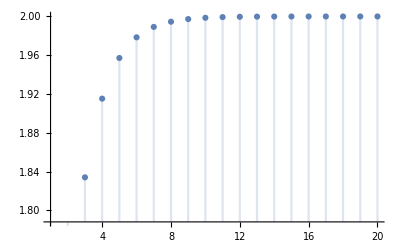

```mathematica
DiscretePlot[2^(1-2^-n),{n,1,20}]
```

While n goes infinity, 2^(1-2^-n) close to a number, so the sequence has limit

Then we calculate the limit

```mathematica
Limit[2^(1-2^-n),n->∞]
```

2

### 1.2

#### i)

f(Limit[1/(n+1),n→∞]) = 1 has exactly 1 solution

Sequence converges

```mathematica
Limit[1/(n+1),n->∞]
```

0

#### ii)

f(Limit[1/n,n→∞]) = 1/0, which is invalid

Sequence converges

```mathematica
Limit[1/n,n->∞]
```

0

#### iii)

f(Limit[Sin[n],n→∞]) no solution because limit does not have solution

```mathematica
Limit[Sin[n],n->∞]
```

Indeterminate

#### iv)

f(Limit[2^((2^n-1)/2^n),n→∞]) has solution 2^(3/4) but sequence diverge

```mathematica
Limit[2^((2^n-1)/2^n),n->∞]
```

2

```mathematica
∑_(n=1)^∞ 2^((2^n-1)/2^n)
```

Sum::div: Sum does not converge.

∑_(n=1)^∞ 2^(2^-n (-1+2^n))

```mathematica
2^((2^2-1)/2^2)
```

2^(3/4)

## 2. Serious series

### 2.1

#### A)

```mathematica
f[_n] = Sin[n]/n
```

We notice a_n>0

```mathematica
Table[Sin[n]/n,{n,1,10}]
```

{Sin[1],Sin[2]/2,Sin[3]/3,Sin[4]/4,Sin[5]/5,Sin[6]/6,Sin[7]/7,Sin[8]/8,Sin[9]/9,Sin[10]/10,Sin[11]/11,Sin[12]/12,Sin[13]/13,Sin[14]/14,Sin[15]/15,Sin[16]/16,Sin[17]/17,Sin[18]/18,Sin[19]/19,Sin[20]/20}

We test (2) the output should be false

```mathematica
Sin[19]/19>Sin[20]/20
```

False

We test (3) should be 0

```mathematica
Limit[Sin[n]/n,n->∞]
```

0

#### B)

```mathematica
f[_n] =1+ 1/n
```

We notice a_n>0

```mathematica
Table[1+ 1/n,{n,1,20}]
```

{2,3/2,4/3,5/4,6/5,7/6,8/7,9/8,10/9,11/10,12/11,13/12,14/13,15/14,16/15,17/16,18/17,19/18,20/19,21/20}

We test (2) the output should be True

```mathematica
20/19>21/20
```

True

We test (3) should not be 0

```mathematica
Limit[1+ 1/n,n->∞]
```

1

### 2.2

#### A)

In this case, I would like to use a converge function and it converge in Abs[]

```mathematica
3(-1)^n/n!
```

(3 (-1)^n)/(n!)

Now we make a graph to show it is converge or not

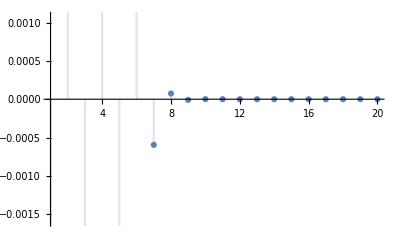

```mathematica
DiscretePlot[(3 (-1)^n)/(n!),{n,1,20}]
```

After we confirm it is converge we calculate the sum

```mathematica
∑_(n=1)^∞ (3 (-1)^n)/(n!)
```

(3 (1-ⅇ))/ⅇ

```mathematica
N[(3 (1-ⅇ))/ⅇ]
```

-1.89636

Then we start calculate the Abs[sum]

```mathematica
∑_(n=1)^∞ Abs[(3 (-1)^n)/(n!)]
```

3 (-1+ⅇ)

```mathematica
N[3 (-1+ⅇ)]
```

5.15485

In this case, with the absolute, the property of series does not change, that means the  absolute value of a_n is continue get closer to a number, however their sum is not equal.

#### B)

We start making a series base on 1/n which is not converge. 
In order to make the series bouncing in positive and negative range
we put(-1)^(n-1) on the top of the 1/n:

```mathematica
(-1)^(n-1)/n
```

Then we calculate does it has sum or not

```mathematica
∑_(n=1)^∞ (-1)^(n-1)/n
```

Log[2]

```mathematica
N[Log[2]]
```

0.693147

Surprisedly, it has sum, and we make a plot of it

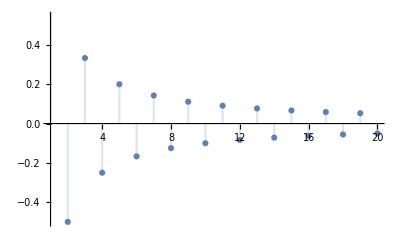

```mathematica
DiscretePlot[(-1)^(n-1)/n,{n,1,20}]
```

Here is the absolute version of example

```mathematica
Abs[(-1)^(n-1)/n]
```

ⅇ^(-π Im[n])/Abs[n]

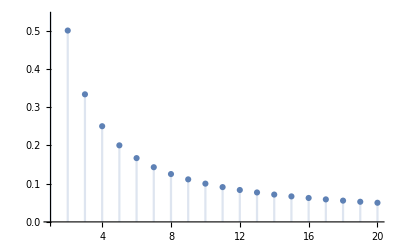

```mathematica
DiscretePlot[ⅇ^(-π Im[n])/Abs[n],{n,1,20}]
```

We can let Mathematica calculate the sum

```mathematica
∑_(n=1)^∞ ⅇ^(-π Im[n])/Abs[n]
```

Sum::div: Sum does not converge.

∑_(n=1)^∞ ⅇ^(-π Im[n])/Abs[n]

We notice on the top of simplify Abs[(-1)^(n-1)/n], it contain Euler’s identity

```mathematica
Abs[(-1)^n]
```

ⅇ^(-π Im[n])

We can conclude that if the absolute of series contain the product of Euler’s identity, like Abs[(-1)^n], and the series is convergent, then the absolute of series is divergent

### 2.3

Here is the example two diverge series can be add up to converge

In the example, we choose two bouncing series but an+bn can be 0, then the whole series converge to 0

```mathematica
Limit[Sin[n],n->∞]
```

Indeterminate

```mathematica
Limit[Sin[n-Pi],n->∞]
```

Indeterminate

```mathematica
Limit[Sin[n]+Sin[n-Pi],n->∞]
```

0

### 2.4

Let’s make a plot of Cos[x]^n

```mathematica
∑_(n=1)^∞ Cos[x]^n
```

-Cos[x]/(-1+Cos[x])

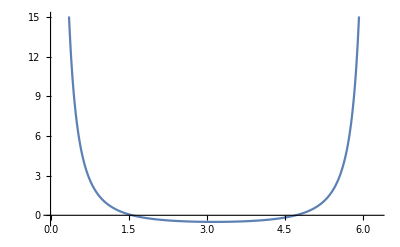

```mathematica
Plot[-Cos[x]/(-1+Cos[x]),{x,0,2Pi}]
```

It seems like in {x,0,π}, Cos[x]^n converge, and in {x,π,2π}, Cos[x]^n diverge

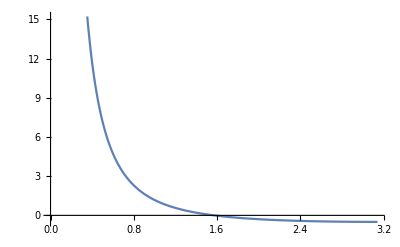

```mathematica
Plot[-Cos[x]/(-1+Cos[x]),{x,0,Pi}]
```

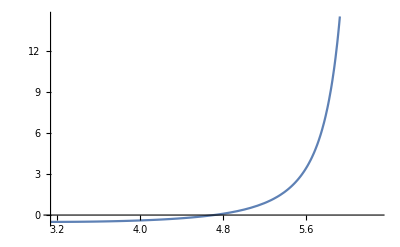

```mathematica
Plot[-Cos[x]/(-1+Cos[x]),{x,Pi,2Pi}]
```

Let just calculate it to prove assumption is true or not

```mathematica
D[-Cos[x]/(-1+Cos[x]),x]
```

Sin[x]/(-1+Cos[x])-(Cos[x] Sin[x])/(-1+Cos[x])^2

```mathematica
Sin[x]/(-1+Cos[x])-(Cos[x] Sin[x])/(-1+Cos[x])^2==0
```

Sin[x]/(-1+Cos[x])-(Cos[x] Sin[x])/(-1+Cos[x])^2==0

```mathematica
Solve[Sin[x]/(-1+Cos[x])-(Cos[x] Sin[x])/(-1+Cos[x])^2==0,{x},Reals]
```

{{x→ConditionalExpression[2 (-π/2+2 π C[1]), C[1]∈ℤ]},{x→ConditionalExpression[2 (π/2+2 π C[1]), C[1]∈ℤ]}}

Therefore, π is the boundary of Cos[x]^n converge and diverge,
In range [(2x)π, (2x+1)π ],
Let try to figure out does it also work in ∑_(n=1)^∞ Cos[x]^n/2^n

```mathematica
∑_(n=1)^∞ Cos[x]^n/2^n
```

-Cos[x]/(-2+Cos[x])

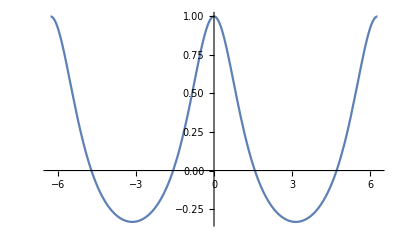

```mathematica
Plot[-Cos[x]/(-2+Cos[x]),{x,-2Pi,2Pi}]
```

```mathematica
D[-Cos[x]/(-2+Cos[x]),x]
```

```mathematica
Sin[x]/(-2+Cos[x])-(Cos[x] Sin[x])/(-2+Cos[x])^2==0
```

Sin[x]/(-2+Cos[x])-(Cos[x] Sin[x])/(-2+Cos[x])^2==0

```mathematica
Solve[Sin[x]/(-2+Cos[x])-(Cos[x] Sin[x])/(-2+Cos[x])^2==0,{x},Reals]
```

{{x→ConditionalExpression[2 π C[1], C[1]∈ℤ]},{x→ConditionalExpression[π+2 π C[1], C[1]∈ℤ]}}

It seems like the ∑_(n=1)^∞ Cos[x]^n/2^n is move away and become converge in range [0,π]

```mathematica
∑_(n=1)^∞ Cos[x]^n/2^n
```

```mathematica
Sum[Cos[x]^n/2^n,{n,1,∞},{x,2 π ,3π}]
```

-(2 (4-Cos[1] Cos[2]-Cos[1] Cos[3]-Cos[2] Cos[3]+Cos[1] Cos[2] Cos[3]))/((-2+Cos[1]) (-2+Cos[2]) (-2+Cos[3]))

```mathematica
N[-(2 (4-Cos[1] Cos[2]-Cos[1] Cos[3]-Cos[2] Cos[3]+Cos[1] Cos[2] Cos[3]))/((-2+Cos[1]) (-2+Cos[2]) (-2+Cos[3]))]
```

0.866809

### 2.5

The best example is the point of the corner never be removed, because we cannot remove the point outside of the square
We set up the S of whole square is 1
S1 = (1/3)^2
S2 = (1/3)^2+8*(1/9)^2
S3 = (1/3)^2+8*(1/9)^2+8^2*(1/27)^2
Sn = 8^(n-1)/9^n
Then we can calculate the sum of this series

```mathematica
∑_(n=1)^∞ 8^(n-1)/9^n
```

1

1-1=0, therefore while the removing point is close to infinity, the whole block will be remove, even there are still points cannot be removed

### 2.6

#### i) First four partial sums

```mathematica
∑_(n=1)^1 n/(n+1)!
```

1/2

```mathematica
∑_(n=1)^2 n/(n+1)!
```

5/6

```mathematica
∑_(n=1)^3 n/(n+1)!
```

23/24

```mathematica
∑_(n=1)^4 n/(n+1)!
```

119/120

#### ii) Show that our series is convergent and evaluate its sum

```mathematica
∑_(n=1)^∞ n/(n+1)!
```

1

In this case, we know the whole sum is getting to 1,
Now we start prove it

We calculate the S[3]

```mathematica
S[3] =  ∑_(n=1)^3 n/(n+1)!
```

23/24

Then we calculate ∫_3^∞ n/((1+n)!)ⅆn

```mathematica
NIntegrate[n/(n+1)!,{n,3,∞}]
```

0.0920188

Then we calculate ∫_(3+1)^∞ n/((1+n)!)ⅆn

```mathematica
NIntegrate[n/(n+1)!,{n,4,∞}]
```

0.0210469

Now we use:
S[3] +∫_(3+1)^∞ n/((1+n)!)ⅆn < S < S[3] + ∫_3^∞ n/((1+n)!)ⅆn

For S[3] +∫_3^∞ n/((1+n)!)ⅆn

```mathematica
23/24+0.0920187627024872
```

1.05035

For S[3] + ∫_(3+1)^∞ n/((1+n)!)ⅆn

```mathematica
23/24+0.021046908746266267
```

0.97938

Therefore:
0.97938 < S < 1.05035
Which means the S(sum) ≈ 1

## 3. A cat and dog game

### A)

```mathematica
cat[x] = ∑_(n=0)^∞ Subscript[C, n] x^n
```

∑_(n=0)^∞ x^n C_n

```mathematica
cat'[x_]
```

∑_(n=0)^∞ n x_^(-1+n) C_n

Due to the first term n!=0, the whole summation start in n=1

```mathematica
∑_(n=1)^∞ n x_^(-1+n) Subscript[C, n];
```

And we can make it turn to start with n=0

```mathematica
∑_(n=0)^∞ (n+1) x_^n Subscript[C, n+1];
```

Now we calculate cat’’(x)

```mathematica
D[∑_(n=0)^∞ (n+1) x_^n Subscript[C, n+1],x_]
```

∑_(n=0)^∞ n (1+n) x_^(-1+n) C_(1+n)

In the same step we make it start with 0, then we get cat’’(x)

```mathematica
∑_(n=0)^∞ (n+1) (2+n) x_^n Subscript[C, 2+n];
```

Due to cat’’(x) = cat(x), we can know

```mathematica
(n+1)(2+n) Subscript[C, 2+n] = Subscript[C, n];
```

Due to cat’(x) = dog(x), we can know

```mathematica
Subscript[d, n]= (n+1) Subscript[C, n+1];
```

```mathematica
Subscript[d, 1] = 1*Subscript[C, 1]==1;
```

Then we know C1 = 1
As we already know cat(0) = 0, which means we know C_0 = 0
We can try to figure out could we put C_0 and C_1 inside of C_n =(n+1)(2+n) C_(2+n);
We can try to find C2

```mathematica
Subscript[C, n] =(n+1)(2+n) Subscript[C, 2+n];
Subscript[C, n]/(n+1)(2+n) = Subscript[C, 2+n];
Subscript[C, 2+n] = Subscript[C, n]/(n+1)(2+n);
Subscript[C, 2] = Subscript[C, 0] /2 ==0;
```

The number is 0, So right here I guess there maybe a relationship between the function and odd/even
Let try let n = 2m (which mean let n is even), and we create a C_(-2m+n) with C_0 and get the result

```mathematica
Subscript[C, n]/(n+1)(2+n) = Subscript[C, 2+n];
Subscript[C, n] = Subscript[C, n-2]/(n-1)(n);
```

Then we find the fourth term step by step:

The third term

```mathematica
D[∑_(n=0)^∞ (n+1) (2+n) x_^n Subscript[C, 2+n],x_]
```

```mathematica
∑_(n=0)^∞ n (1+n) (2+n) x_^(-1+n) Subscript[C, 2+n]
```

```mathematica
∑_(n=0)^∞ (1+n) (2+n) (3+n) x_^n Subscript[C, 3+n]
```

The fourth term:

```mathematica
D[∑_(n=0)^∞ (1+n) (2+n) (3+n) x_^n Subscript[C, 3+n],x_]
```

∑_(n=0)^∞ n (1+n) (2+n) (3+n) x_^(-1+n) C_(3+n)

```mathematica
∑_(n=0)^∞ (1+n) (2+n) (3+n) (4+n) x_^n Subscript[C, 4+n]
```

Then we find the order of even term:

```mathematica
Subscript[C, n] = Subscript[C, n-4]/n(n-1)(n-2)(n-3);
...
Subscript[C, n] = Subscript[C, n-2m]/n(n-1)(n-2)...(n-2m+1)
     = Subscript[C, 0]/n!
     = 0;
```

While n is even, Cn = 0. 
Now with n = 2m+1 we know it going to be C1 on the top and n on the bottom
and the process is going to be the same so I directly show it:

```mathematica
Subscript[C, n]= Subscript[C, 1]/n!
```

We already know C1 = 1:

```mathematica
Subscript[C, n]= 1/n!
```

After we got cat, we can find dog base on d_n= (n+1) C_(n+1)
While n = 2m

```mathematica
Subscript[d, 2m]= (2m+1) Subscript[C, 2m+1] =(2m+1)* 1/(2m+1)! = 1/(2m)!
```

Therefore we know while n is even

```mathematica
Subscript[d, n]= 1/n!
```

In the same way, we can know while n is odd

```mathematica
Subscript[d, n]= 0
```

In conclusion:
C_n=0 	    (n is even)
C_n= 1/n!  (n is odd)
d_n= 0 	    (n is odd)
d_n= 1/n!  (n is even)

### B)

Find e^x and e^-x

```mathematica
Series[Exp[x],{x,0,5}]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+O[x]^6

```mathematica
Series[Exp[-x],{x,0,5}]
```

1-x+x^2/2-x^3/6+x^4/24-x^5/120+O[x]^6

And we get sequence of cat and dog base on a)

cat(x) = (x^1/(1!)+x^3/(3!)+x^5/(5!)+ ...)
dog(x)= (1+x^2/2+x^4/(4!)+...)

And then we can know:
e^x   =  cat(x) +dog(x)
e^-x =  -cat(x) +dog(x)

### C)

#### Dog(x)

e^-x =  -cat(x) +dog(x)
Then:
dog(x) = e^-x-cat(x)
And:
dog(x) =  cat(x) - e^x 
So:
2dog(x) =e^-x- (- e^x )
Result:
dog(x) = (e^-x+ e^x )/2

#### Cat(x)

e^-x =  -cat(x) +dog(x)
Then:
 cat(x)  =  dog(x) - e^-x 
 cat(x) =  e^x  -dog(x) 
 So:
 2 cat(x) = e^x - e^-x 
 Result:
 cat(x) = (e^x - e^-x )/2

### D)

#### Plot cat(x) and first four different partial sums of its power series

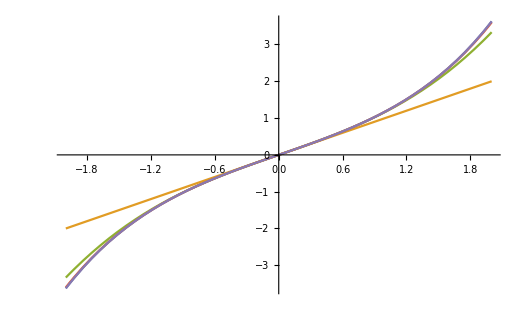

```mathematica
Plot[{1/2 (-Exp[-x]+Exp[x]),x,x+x^3/(3!),x+x^3/(3!)+x^5/(5!),x+x^3/(3!)+x^5/(5!)+x^7/(7!)},{x,-2,2}]
```